# Money

A short discussion on the circulation of money in a network

Leanne Ussher, Jun. 30,  2018

Money is not well understood. Most text books argue that it is based on trust and its value is determined by supply and demand. While this is true, they often omit to mention that money is constantly being created and destroyed by the entities licensed to make the money. In the case of the US dollar it these are the Federal Reserve, commercial banks, and the federal government.  No other entities by law can create  US legal tender, money stock M1. However, the private creation of  complementary currencies are possible. We see this in the popular rise of crypto currencies. Non digital local currencies have also existed for centuries. In this paper we discuss what a monetary circuit is and a network of an experiment in creating a complementary currency in the Berkshire’s in 1992.

## Fiat Money

A common definition of fiat money is:

```mathematica
Entity["Word","fiat money"][EntityProperty["Word","Definitions"]]
```

{{fiat money,Noun}→money that the government declares to be legal tender although it cannot be converted into standard specie}

It seems strange to some that money can be created from nothing, but through the power of a government to impose usage through law   and taxation, fiat or sovereign money becomes stable and valuable as a medium of exchange.

Fiat Currency is an IOU (I owe you). Its supply or measurement is called M1. The M1 money stock that exists at any one point in time primarily consists of

1) federal notes (green backs) which are in circulation (outside of bank vaults); and

2) bank deposits.

In all cases this money is created from nothing,  the Federal reserve creates the former, while banks create the latter. Indeed as Hyman Minsky once said “anyone can create money; the problem is to get it accepted”.

A plot of the stock of money or M1 over time is below.

```mathematica
WolframAlpha["plot money supply m1",IncludePods->{"History:MoneySupply:EconomicData"}]
```

WolframAlphaQueryResults

## Velocity of Fiat Money

Each time money circulates (quantity of money times the number of transactions) it is in exchange for goods or services (price times quantity) we can write this as an equation, where money velocity equals total transactions:

M.V = P.Y                        where  M=M1, V = Velocity , P = price, Y = quantity of goods and services.

The circulation of money is easiest to understand in a closed network with just trade, and in this case we do not have a central bank or commercial banks. In the flow graph below the Government is both source and sink. At the top  - GovernmentSpend - injects money into the system. At the bottom -GovernmentTax-  extinguishes the currency from the system through taxing. The management of injection and extraction of money is done in a way to keep the value of money stable: ie. to ensure the money supply equals money demand at the targeted price.

In this overly simplified graph below  the Government injects 120 units of cash into the network - the green directed links. These 120 units can circulate around the network from node to node, creating transactions as it goes. At at each point the money is either hoarded (not spent) or passed on into circulation through the system.   Infinite loops could occur in this graph, however here we have specified the total circulation across each link by giving its capacity and residual hoards.  The Government removes part of the money stock by the red directed links.

A graph with source and sink:

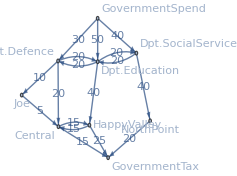
```mathematica
h=-Graphics-;PropertyValue[{h,Cases[EdgeList[h],"GovernmentSpend"->_]},EdgeStyle]=Green;PropertyValue[{h,Cases[EdgeList[h],_->"GovernmentTax"]},EdgeStyle]=Red;
```

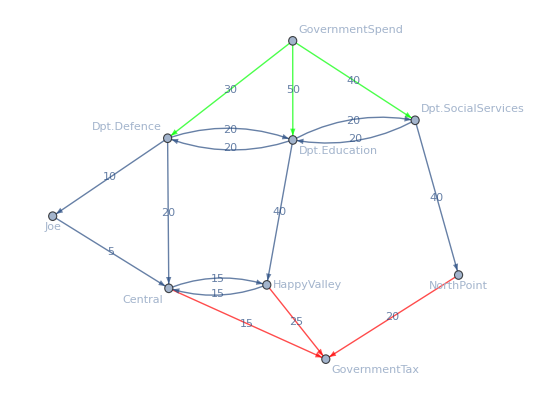

```mathematica
h
```

In this case we have the following transactions, giving us an aggregate number of injections, transactions or velocity of money, leakages, and taxes.

```mathematica
mv=Total[PropertyValue[{h,#},EdgeCapacity]&/@EdgeList[h]];
govtS=Total[PropertyValue[{h,#},EdgeCapacity]&/@Cases[EdgeList[h],"GovernmentSpend"->_]];
govtT=Total[PropertyValue[{h,#},EdgeCapacity]&/@Cases[EdgeList[h],_->"GovernmentTax"]];
MapThread[List,{{"Government Spending", "M.V","Leakages","Taxes"},{govtS,mv,govtS-govtT,govtT}}]//Prepend[#,{"Flows",""}]&//Grid[#,Alignment->{{Left,Decimal}},Dividers->{None,{False,True,False}}]&//Framed
```

Flows | 
Government Spending | 120
M.V | 405
Leakages | 60
Taxes | 60

We can also calculate the velocity of money as

P.Y/M = V

```mathematica
405/120.
closeInputCell[]
```

3.375

In this simple network money is conserved, ie. the stock of money M1 remains constant when it is not being changed by the Government. The money does not circulate more because there are some nodes in the network that hoard money and reduce velocity.

Leakages

Joe | 5
NorthPoint | 20
Happy Valley | 15
Dpt.Ed | 10
Central | 10

## A Local Currency

In an economy where there are net leakages, (e.g. from net imports, or net financial outflows) and spare capacity,  it may be warranted to create a complementary community currency. The local currency is typically not exchangeable into the national currency. As a result once the currency is issued it cannot leave except through hoarding or some other structural architecture instituted by the issuer to extguish it such as fees, taxes, or expiration dates.

### The Berkshire Local Currency Experiment

In Summer of 1992 the main street of Great Barrington trialed an experiment to see if a local currency could increase spending and income in the township. Each business had to pay a membership fee of US$75. They were given fungible coupons at the beginning of the summer to give to their customers. Every $10 a customer spent they got a Berkshare currency equivalent to the spending power of one USD. At the end of the summer there was a 3 day period in which the coupons could be spent at the businesses in main street. Each business got to set their terms e.g. each customer could use the coupons for a maximum of 50% of the sale price, or up to 100% of the sale price during the 3 day period. At the end of the 3 days the Berkshares would expire worthless.  The stores had to keep a record of the number of  Berkshares which they issued and signed. The total number of Berkshares received at the end of the 3 days of sales were collected and tallied, noting from which store they originated.

Below is a network of the Berkshare community currency with the links directed from issuing source to collecting sink. Self links have been removed. Each node is a business on Main Street in Great Barrington. The graph is grouped into shops that have similar connections.

Community Graph of Berkshare Data.

Hovering over the nodes will give store names.

```mathematica
CommunityGraphPlot[Graph[MapThread[Tooltip,{VertexList[g],nameList}],EdgeList[g]]]
```

-Graphics-

The conclusion from this experiment was that money circulates a lot from one business to another. This experiment was deemed a success in educating the shopkeepers of the value fo a community currency. In 2010 an actual Berkshare currency (backed by US dollars) was created.

## Author contact information

Leanne Ussher

ussher@gmail.com

## Initializations

```mathematica
(* a representative graph of half of the Berkshire network - businesses A through M. Data obtained from the Schumacher Center for New Economics *)g=SimpleGraph@AdjacencyGraph[{{7,0,0,0,11,0,0,0,0,0,0,0,0,6,8,0,0,0,0,0,0,10,0,12,0,0,0,0,0,0,0,0,0,0,17,0,0,0,0,0,9,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,3,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,2,0,0,0,0,0,0,2,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,7,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,4,0,458,0,0,0,0,24,0,2,10,4,3,0,27,1,0,0,0,45,5,15,0,12,5,2,9,49,0,0,0,0,27,0,0,0,34,3,8,0,0,7,3,0,0,0},{0,1,0,0,1,15,0,0,0,3,0,0,0,9,4,2,7,3,0,0,0,6,0,15,0,0,15,8,4,4,0,0,0,0,28,1,0,2,1,4,8,1,1,1,1,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,2,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,2,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,2,2,0,0,5,7,0,4,2,91,6,0,7,3,0,0,0,6,1,55,0,1,0,0,0,11,0,0,0,0,23,0,0,0,12,0,1,2,0,11,0,0,0,0},{0,0,0,0,13,0,0,0,0,48,0,3,5,0,2,10,0,4,6,0,0,16,0,0,0,0,12,0,2,6,0,0,0,0,5,0,0,29,0,0,4,6,0,10,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,2,0,0,0,19,4,10,0,0,3,2,0,0,0,2,0,0,0,0,0,0,0,0,18,0,0,0,0,0,0,3,0,0,28,0,0,0,0,0,0,0},{0,0,0,0,7,0,0,1,1,0,0,40,42,9,0,0,2,0,0,0,0,2,0,2,0,0,0,0,0,0,0,0,0,0,2,2,0,1,0,1,0,3,0,0,0,0,0,0},{0,2,0,1,9,1,0,0,2,23,0,0,14,511,10,0,0,7,0,0,0,27,3,61,0,17,6,2,5,19,8,0,0,0,39,8,0,0,64,7,2,8,2,22,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,7,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,4,45,0,0,0,0,4,0,0,0,0,0,1,0,0,0,0,5,0,2,0,0,0,0,5,0,1,2,1,3,0,0,0},{0,0,4,0,0,3,0,2,0,1,0,0,4,3,1,0,6,24,0,0,0,3,2,2,0,2,5,0,0,3,0,0,1,0,8,0,0,3,4,0,3,2,2,3,2,0,3,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,4,0,0,16,0,18,0,0,1,0,12,0,0,2,0,0,0,0,0,0,0,4,0,0,0,0,0,0,0,0,8,0,0,0,0},{0,0,0,0,5,0,0,0,0,0,0,0,5,5,9,0,0,0,0,0,0,0,0,3,0,50,0,0,0,0,0,0,0,0,16,12,0,0,0,0,0,0,0,9,0,0,0,0},{0,0,7,0,3,0,0,1,0,0,0,0,19,0,104,0,7,1,0,0,0,6,0,37,0,0,5,0,0,9,0,0,0,0,3,0,0,0,0,8,0,1,0,0,0,2,0,0},{0,1,12,0,13,0,0,0,1,22,0,3,4,21,17,0,10,11,0,0,0,381,1,14,5,33,31,12,0,7,0,0,0,0,42,0,0,1,3,1,0,13,16,41,3,2,0,0},{0,2,0,0,28,0,0,0,0,22,0,8,3,7,16,0,9,6,0,2,0,25,10,0,0,2,12,0,21,17,21,0,6,0,12,0,0,43,0,7,0,7,0,31,4,5,0,0},{0,0,0,0,25,3,0,0,0,28,0,4,20,76,3,0,0,10,0,9,0,28,0,223,57,54,20,0,10,1,0,0,5,0,32,0,0,0,53,5,46,10,10,27,6,2,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,18,0,0,0,0,28,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,4,0,8,3,0,0,2,21,0,0,11,15,4,15,5,4,0,0,0,29,0,16,0,16,82,0,0,10,0,0,3,0,46,0,0,16,20,12,13,12,0,10,2,0,40,0},{0,0,4,0,0,0,0,0,1,0,0,1,10,19,0,2,2,3,0,0,0,11,0,6,0,0,5,48,0,2,0,0,0,0,12,0,0,6,0,1,20,3,0,12,0,0,1,0},{0,0,0,10,0,0,0,0,0,0,0,9,0,2,0,0,0,0,0,0,0,0,0,0,62,0,0,0,34,5,0,0,0,0,1,0,0,0,0,3,15,3,8,0,0,0,0,0},{4,3,1,0,0,1,0,0,8,5,0,0,12,6,7,0,3,3,0,8,1,12,1,0,0,5,3,0,0,17,0,1,4,0,13,9,0,0,1,5,15,4,0,1,2,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,3,0,9,1,0,3,0,2,0,0,9,20,6,0,0,1,0,0,0,8,0,2,0,2,11,0,0,6,0,5,0,0,22,0,0,0,0,0,2,0,0,7,2,0,0,0},{0,1,3,0,9,0,0,0,1,8,0,0,2,5,0,0,0,1,0,0,0,4,0,2,0,8,7,0,0,17,0,0,44,0,11,0,0,0,0,0,9,0,0,0,1,2,0,0},{0,11,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,19,0,98,14,0,0,2,45,0,23,43,37,23,0,0,16,25,22,1,127,8,48,37,32,51,9,25,29,20,0,19,0,1322,25,0,13,65,25,17,39,45,16,17,17,6,0},{0,0,0,0,6,0,0,0,0,2,0,0,12,0,0,0,7,0,0,0,0,0,0,2,0,11,0,0,0,0,0,0,0,0,5,3,0,0,0,0,18,5,7,17,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,6,0,0,0,0,0},{0,1,0,0,36,0,0,0,5,36,0,123,7,28,17,0,7,1,0,0,0,26,1,8,16,94,19,6,3,24,19,0,0,0,39,5,0,5,404,12,3,10,0,15,6,6,3,0},{0,0,0,0,0,1,0,0,0,2,0,0,2,0,9,0,2,0,0,0,0,0,0,3,0,0,12,0,0,0,0,0,0,0,4,0,0,6,0,5,1,0,9,2,0,0,0,0},{0,0,0,0,0,0,0,5,0,5,0,0,0,23,3,0,0,9,0,0,0,10,0,0,0,14,10,0,0,0,5,0,1,0,58,0,0,21,0,0,114,1,11,7,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,14,0,4,5,0,0,2,0,0,0,0,0,26,0,0,2,0,0,0,0,0,0,0,0,0,0,0,1,5,0,56,0,4,0,0,0,0},{0,1,0,0,3,0,0,0,2,6,0,0,1,6,0,0,30,4,0,0,0,20,0,0,0,0,0,0,8,1,0,0,4,0,5,2,0,0,0,0,0,0,2,0,0,0,0,0},{0,0,0,0,10,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,26,0,0,0,0,0,0,0,0,15,0,0,0,6,0,3,0,3,3,0,11,0,0},{0,0,9,0,10,0,0,0,2,0,0,19,12,14,0,0,0,0,0,0,0,14,9,7,0,0,4,0,9,10,4,0,0,0,26,0,0,0,2,11,0,2,0,6,33,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,14,0,8,0,0,0,0,0,0,0,32,0,0,0,19,2,0,0,0,0,0,0,0,7,0,0,0,0,0,0,0,0,0,0,0,40,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}];nameList={"Animal Presence","Baker's wife","Barrington Ballet","Beckwhith's Glass","Berkshire Child","Berkshire Coffee","Berkshire Craft","Berkshire Cupboard","Bill's Pharmacy","Byzantium","Cabinet Works","Caligari's","Captain Toss","Carr Bros HDWE","Castle St. Café","Harry Conklin","Crystal Essence","Daily Bread","decades","Diva","Dolby Florist","EverGreen","Farshaw's","Frames on Wheels","Galeria Arriba","Gans Appliance","Gatby's","Gorham & Norton","Harland Foster","Herbert's Shoes","Home Textures","Impoco's Video","Initially Yours","Inn at Green River","Jack's","Jillifers","Jodi's","Kahn's","Krol Jewelers","La Tomate","Lamplighter","Laramee Cleaners","Leatherwoods","Main st Clothing","Manhattan Pizza","Mamphis Hair","Mill River Studio","Monument Mt"};vertexNames=Flatten[Position[nameList,#]][[1]]->#&/@nameList;
```